## 3강 함수와 그래프

전경원<ruddyscent@gmail.com>

2014년 9월 2일 화요일

## 함수 정의하기

```mathematica
Log[1]
```

```mathematica
f[x_]:=x^2+2x-4
```

```mathematica
f[1]
```

```mathematica
f[π]
```

```mathematica
inv[x_]:=1/x
```

```mathematica
inv[45]
```

```mathematica
g[x_]:=N[inv[x]]
```

#### 함수를 정의하는 방법

함수 이름은 반드시 소문자로 시작하도록 정한다. 매스매티카 내장 함수의 이름은 대분자로 시작하므로 내장 함수 이름과 충돌하는 일을 방지할 수 있다.

함수 정의의 왼쪽에 있는 매개변수에 언더스코어를 붙인다.

함수의 매개변수는 [과 ]로 둘러싼다.

함수 정의의 왼쪽과 오른쪽은 :=로 연결한다.

### 함수 삭제하기

```mathematica
?f
```

```mathematica
Clear[f]
```

```mathematica
?f
```

## 그래프 그리기

```mathematica
Clear[f];
f[x_]:=x^2-2x+4
```

```mathematica
Plot[f[x],{x,-1,3}]
```

```mathematica
Plot[f[x],{x,1.9,2.1}]
```

```mathematica
With[{δ=10^-10},Plot[f[x],{x,2-δ,2+δ}]]
```

```mathematica
Clear[f];
f[x_]:=(x^5-4 x^2+1)/(x-1/2)
```

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Plot[f[x],{x,-1,2},Exclusions->1/2]
```

### 실습

다음 함수를 -10≤x≤10 범위에서 그래프를 그려보세요.

Sin(1+Cos(x))

Sin(1.4+Cos(x))

Sin(π/2+Cos(x))

Sin(2+Cos(x))

## Plot 함수의 옵션

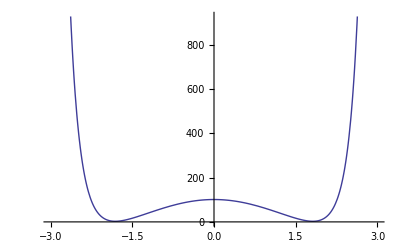

```mathematica
Plot[100Cos[x]+ⅇ^(x^2),{x,-3,3}]
```

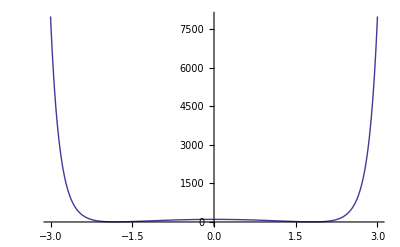

```mathematica
Plot[100Cos[x]+ⅇ^(x^2),{x,-3,3},PlotRange->All]
```

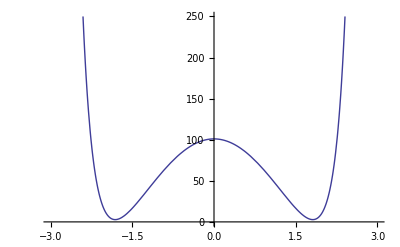

```mathematica
Plot[100Cos[x]+ⅇ^(x^2),{x,-3,3},PlotRange->{0,250}]
```

#### 실습

그래프를 이용하여 x=2에서의 함수 f(x)=√x 근삿값을 찾아보세요.

### 두 축에 동일 비율을 사용하려면

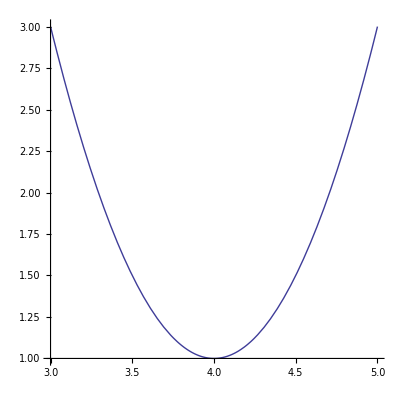

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->Automatic]
```

### 두 축이 원점을 교차하도록 하려면

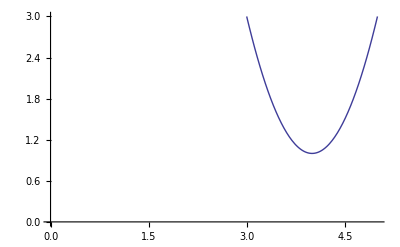

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesOrigin->{0,0}]
```

### 매시 포인트을 보이려면

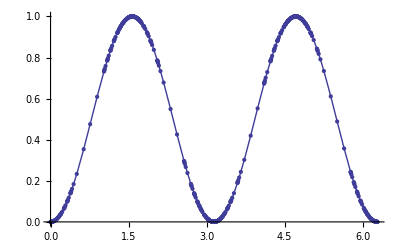

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->All]
```

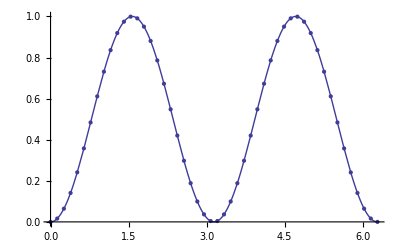

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->Full]
```

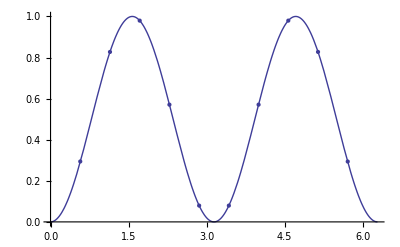

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->10]
```

### 색과 스타일을 바꾸려면

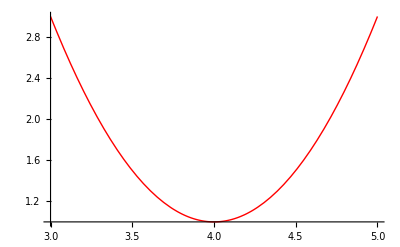

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Red]
```

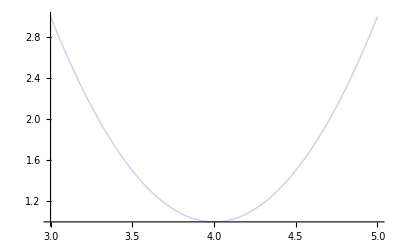

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Lighter[Blue,.8]]
```

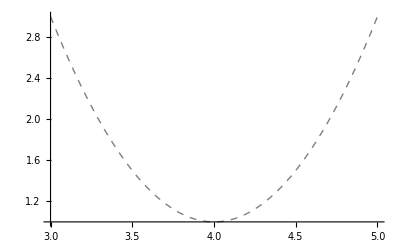

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashed]]
```

### 축을 없애고 테두리를 넣으려면

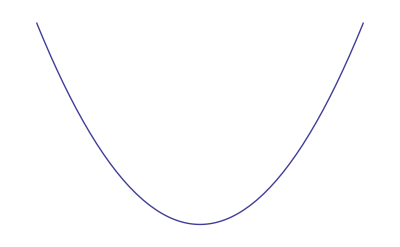

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Axes->False]
```

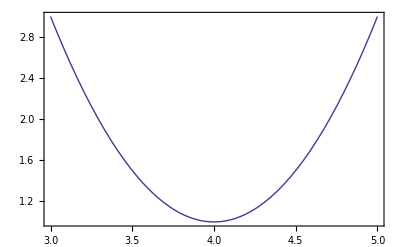

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Frame->True]
```

#### 실습

Axes, Frame, Filling, FrameStyle, PlotRange, AspectRatio 등의 옵션을 사용하여 y=(Cos(15x))/(1+x^2)의 그래프를 다음과 같이 그려보세요.

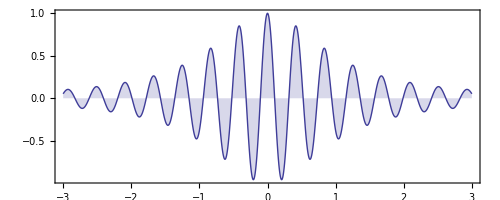

### 축에 화살표를 사용하려면

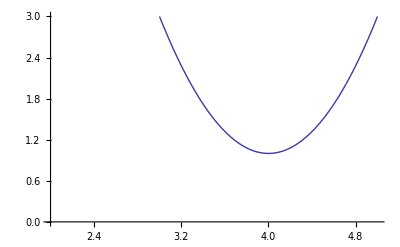

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[.05],AxesOrigin->{2,0}]
```

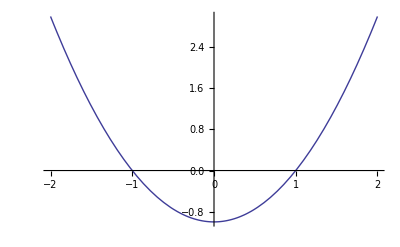

```mathematica
Plot[x^2-1,{x,-2,2},AxesStyle->Arrowheads[{-.05,.05}]]
```

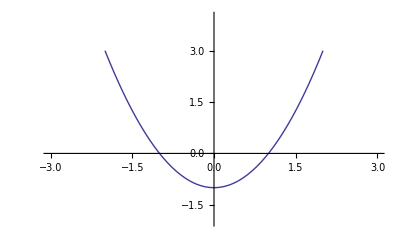

```mathematica
Plot[x^2-1,{x,-2,2},AxesStyle->Arrowheads[{-.05,.05}],PlotRange->{{-3,3},{-2,4}}]
```

### 삼각함수의 그래프 그리기

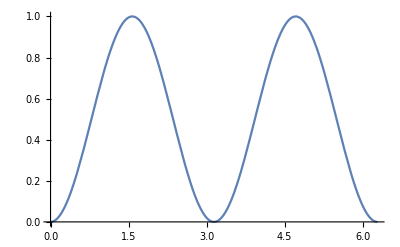

```mathematica
Plot[Sin[x]^2,{x,0,2π}]
```

#### 축의 눈금을 조정하려면

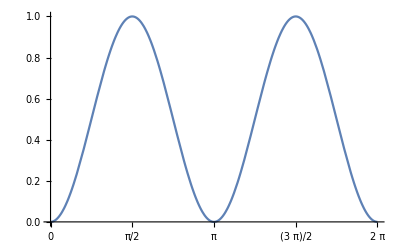

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic}]
```

#### 격자를 사용하려면

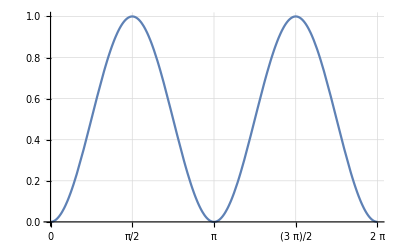

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic},GridLines->Automatic]
```

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic},GridLines->{{π/2,π,(3π)/2,2π},{.2,.4,.6,.8,1}}]
```

-Graphics-

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic},GridLines->{{π/2,π,(3π)/2,2π},{.2,.4,.6,.8,1}},GridLinesStyle->Directive[Thin,Gray,Dotted]]
```

-Graphics-

#### 라벨을 추가하려면

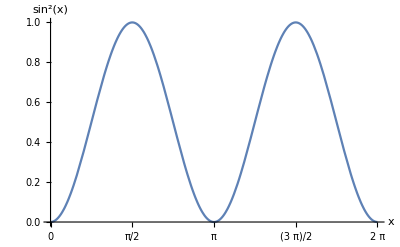

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic},GridLines->{{π/2,π,(3π)/2,2π},{.2,.4,.6,.8,1}},GridLinesStyle->Directive[Thin,Gray,Dotted],AxesLabel->{x,Sin[x]^2}]
```

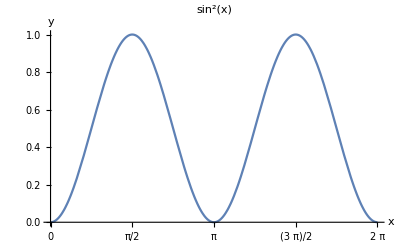

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic},GridLines->{{π/2,π,(3π)/2,2π},{.2,.4,.6,.8,1}},GridLinesStyle->Directive[Thin,Gray,Dotted],AxesLabel->{x,y},PlotLabel->Sin[x]^2]
```

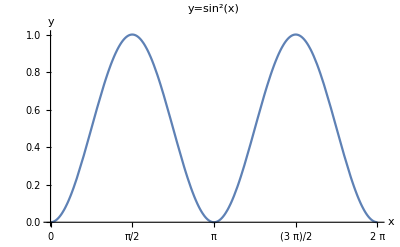

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{Range[0,2π,π/2],Automatic},GridLines->{{π/2,π,(3π)/2,2π},{.2,.4,.6,.8,1}},GridLinesStyle->Directive[Thin,Gray,Dotted],AxesLabel->{x,y},PlotLabel->"y=sin^2(x)"]
```

### 제외와 수직 점근선

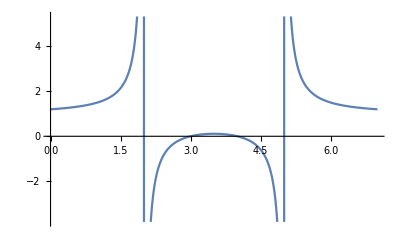

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7}]
```

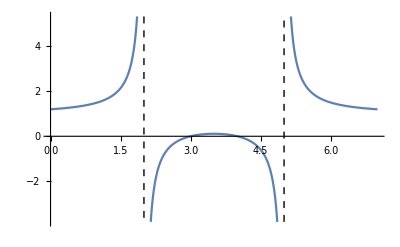

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7},Exclusions->{x==2,x==5},ExclusionsStyle->Dashed]
```

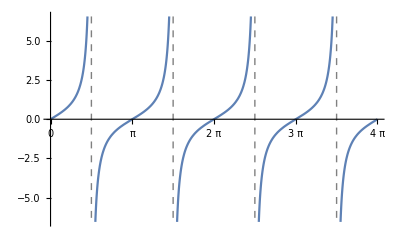

```mathematica
Plot[Tan[x],{x,0,4π},Exclusions->{Cos[x]==0},ExclusionsStyle->Directive[Gray,Dashed],Ticks->{Range[0,4π,π/2],Automatic}]
```

### 로그 비율을 사용하려면

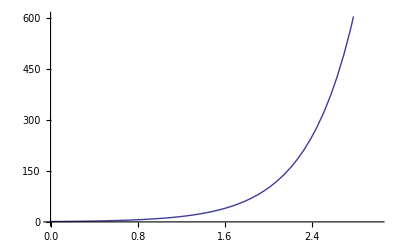

```mathematica
Plot[10^x,{x,0,3}]
```

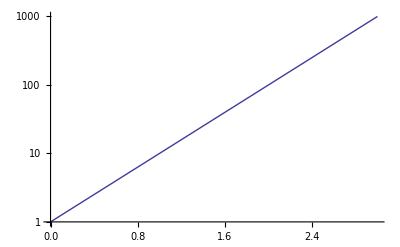

```mathematica
LogPlot[10^x,{x,0,3}]
```

#### 실습

Mesh와 MeshFunctions 옵션을 이용하여 sin(2x)와 1/2 cos(5x)의 교점을 표현하는 그래프를 그리시오.

```mathematica
Plot[
{Sin[2x],1/2 Cos[5x]},
{x,0,2π},
Mesh->{{0}},
MeshFunctions->{Sin[2#1]-1/2 Cos[5#1]&},
MeshStyle->Directive[Red,PointSize[Large]]
]
```

## Manipulate로 함수 관찰하기

```mathematica
Manipulate[x^2,{x,1,10}]
```

```mathematica
Manipulate[x^2,{x,0,50,5}]
```

```mathematica
Manipulate[Plot[x Sin[1/x],{x,0,r}],{r,.1,2}]
```

명령문이 길어진다면, 적절히 줄을 바꾸어서 읽기 편하도록 적는다. r의 범위는 Plot 반복자의 범위가 0이 되지 않도록 작은 양수로 시작한다.

```mathematica
Manipulate[
Plot[x Sin[1/x],{x,0,r}],
{{r,0.2,"right endpoint"},10^-10,2}
]
```

```mathematica
Manipulate[
Plot[a(x-b)^2+c,{x,-5,5},
PlotRange->5,PlotLabel->"y=a(x-b)^2+c"
],
{a,-1,1},
{{b,-1},-3,3},
{{c,2},-3,3}
]
```

```mathematica
Manipulate[
Plot[Sin[4/x],{x,-2π,2π},
PlotPoints->pp,MaxRecursion->mr,Mesh->m],
{{pp,64,"PlotPoints"},{4,8,16,32,64}},
{{mr,4,"MaxRecursion"},{0,1,2,3,4}},
{{m,Full,"Mesh"},{Full,All,None}}
]
```

```mathematica
Manipulate[
Plot[f[x],{x,0,4π},
Ticks->{Range[0,4π,π/2],Automatic},PlotLabel->ToString[f]~~"[x]"],
{{f,Tan,"function"},{Sin,Cos,Sec,Csc,Tan,Cot},ControlType->SetterBar}
]
```

### 바람직한 Manipulate 사용법

변수 이름은 변수의 용도를 잘 나타내도록 정한다.

자세한 지식 없이도 실행해 볼 수 있도록 초깃값을 정한다.

```mathematica
Manipulate[
Plot[Sin[x],{x,0,2π},
Background->RGBColor[red,green,blue]],
{{red,.8},0,1},
{{green,1},0,1},
{blue,0,1}]
```

```mathematica
Manipulate[
Plot[Sin[x],{x,0,2π},Background->Hue[hue,saturation,brightness]],
{hue,0,1},
{{saturation,1},0,1},
{{brightness,1},0,1}]
```

## 테이블 사용하기

```mathematica
f[x_]:=x^2
```

x에 1부터 10까지 정수를 대입

```mathematica
Table[f[x],{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

x를 5씩 증가시키려면,

```mathematica
Table[f[x],{x,0,50,5}]
```

{0,25,100,225,400,625,900,1225,1600,2025,2500}

1부터 시작한다면 시작값 생략해도 된다.

```mathematica
Table[f[x],{x,10}]
```

{1,4,9,16,25,36,49,64,81,100}

특정 x를 대입하려면,

```mathematica
Table[f[x],{x,{1,7,12,20}}]
```

{1,49,144,400}

데이터를 생성하고,

```mathematica
data=Table[{x,f[x]},{x,5}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25}}

표로 표시하려면

```mathematica
Grid[data]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

오른쪽 정렬

```mathematica
Text@Grid[data,Alignment->Right]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

제목줄을 추가하려면,

```mathematica
tableContents=Prepend[data,{"x","x^2"}]
```

{{x,x^2},{1,1},{2,4},{3,9},{4,16},{5,25}}

```mathematica
Text@Grid[tableContents,Alignment->Right,Dividers->{Center,{False,True
}},Spacings->2]
```

x | x^2
1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

```mathematica
Text@Grid[tableContents,Alignment->Right,Dividers->{2->True,2->True},Spacings->2,ItemStyle->{{},{Bold,None}}]
```

x | x^2
1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

#### 괄호의 용법

() | 연산의 우선순의 지정
[] | 함수의 매개변수 지정
{} | 리스트 정의

## 그리드 조정하기

```mathematica
Manipulate[
Text@Grid[{{"C","F"},{c,1.8c+32}},
Dividers->All,ItemSize->5
],
{{c,0},-40,1000,1}
]
```

```mathematica
Manipulate[
Text@Grid[{{"C","F"},
{First@Quantity[c,"DegreesCelcius"],
First@UnitConvert[Quantity[c,"DegreesCelcius"],"DegreesFahrenheit"]
}
},
Dividers->All,ItemSize->5
],
{{c,0},-40,1000,1}
]
```

#### 실습

1부터 100까지의 수로 표를 만들어보자. 한 행에는 숫자가 10개씩 배열되고, 모든 정수는 빨간색으로 나타내야 한다.

```mathematica
Grid@Partition[Table[If[PrimeQ[n],Style[n,Red],n],{n,100}],10]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

## 구간별로 정의된 함수

```mathematica
f[x_]:=Piecewise[{{x, 0≤x≤1}, {-x, -1<x<0}, {1, True}}]
```

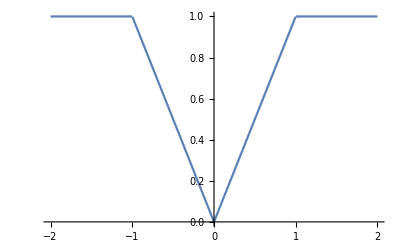

```mathematica
Plot[f[x],{x,-2,2}]
```

InputForm으로 표현하면,

```mathematica
f[x_]:=Piecewise[{{x,0≤x≤1},{-x,-1<x<0}},1]
```

다음 두 개의 함수 정의는 같은 함수를 나타낸다.

```mathematica
g[x_]:=Piecewise[{{x^2, (-2≤x≤-1)||(1≤x≤2)}, {1, -1<x<1}, {4, True}}]
```

```mathematica
g[x_]:=Piecewise[{{x^2, 1≤Abs[x]≤2}, {1, Abs[x]<1}, {4, True}}]
```

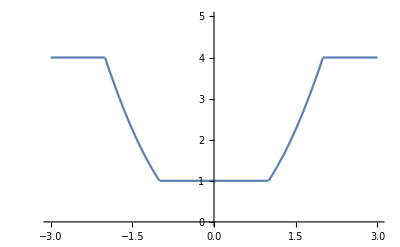

```mathematica
Plot[g[x],{x,-3,3},PlotRange->{0,5}]
```

Plot은 구간 간의 불연속점을 끊어서 보여준다.

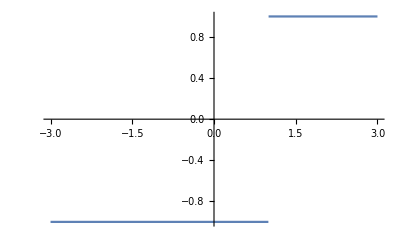

```mathematica
Plot[Piecewise[{{1, x≥1}, {-1, x<1}}],{x,-3,3}]
```

불연속 점을 연결하고 싶다면,

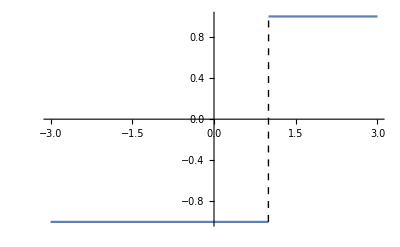

```mathematica
Plot[Piecewise[{{1, x≥1}, {-1, x<1}}],{x,-3,3},ExclusionsStyle->Dashed]
```

## 음함수의 그래프

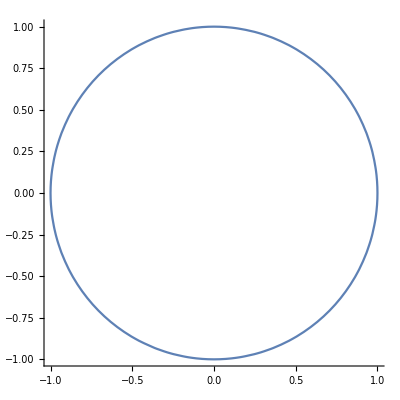

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},Frame->False,Axes->True]
```

그래프 관련 명령어가 복잡한 그래프를 잘 그리지 못한다면, 초기 시도점 개수를 늘려본다.

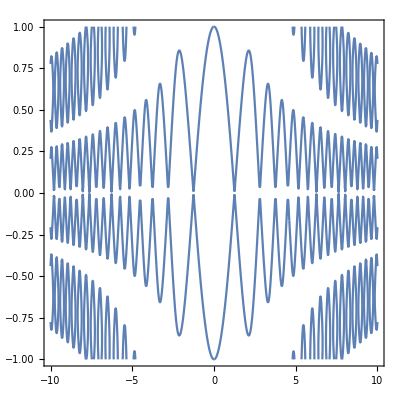

```mathematica
ContourPlot[Sin[x^2]+y^2==Cos[x y],{x,-10,10},{y,-1,1},PlotPoints->100]
```

## 그래프 겹쳐 그리기

### 그래프의 중첩

```mathematica
Clear[f,g];
f[x_]:=1-x;
g[x_]:=x^2;
```

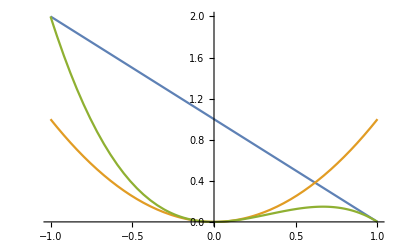

```mathematica
Plot[{f[x],g[x],f[x]g[x]},{x,-1,1}]
```

```mathematica
Plot[Tooltip[{f[x],g[x],f[x]g[x]}],{x,-1,1}]
```

-Graphics-

### 색으로 채우기

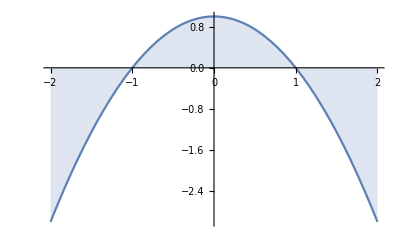

```mathematica
Plot[1-x^2,{x,-2,2},Filling->Axis]
```

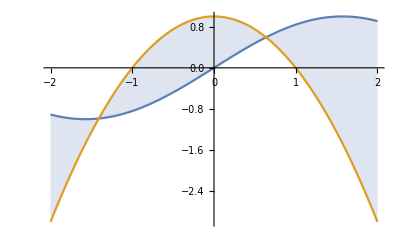

```mathematica
Plot[{Sin[x],1-x^2},{x,-2,2},Filling->{2}]
```

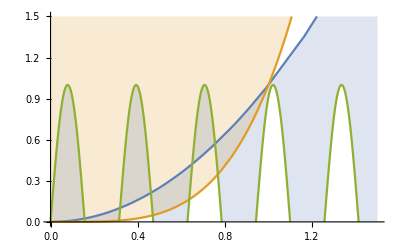

```mathematica
Plot[{x^2,x^4,Sin[20x]},{x,0,1.5},PlotRange->{0,1.5},Filling->{1->{3},2->Top},PlotPoints->10]
```

## 그래픽 다듬기

Line 명령은 점 리스트로 선분을 정의한다.

```mathematica
Line[{{0,0},{1,1},{2,0}}]
```

Line[{{0,0},{1,1},{2,0}}]

그림으로 그리려면, Graphics 명령을 이용한다.

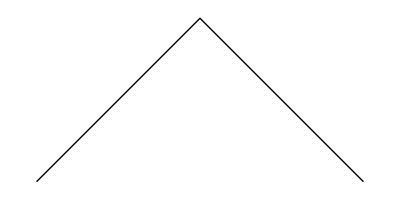

```mathematica
Graphics[Line[{{0,0},{1,1},{2,0}}]]
```

Directive 명령으로 도형의 외형을 변형할 수 있다.

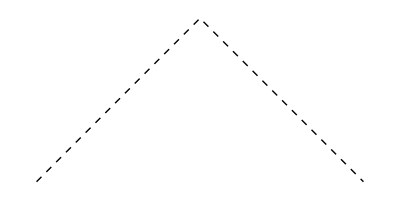

```mathematica
Graphics[{Directive[Thick,Dashed],Line[{{0,0},{1,1},{2,0}}]}]
```

Plot에 사용하던 옵션을 Graphics에도 대부분 사용할 수 있다.

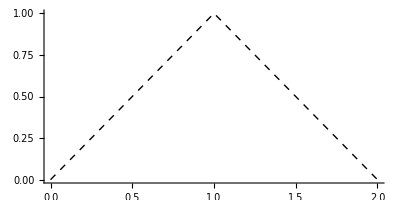

```mathematica
Graphics[{Directive[Thick,Dashed],Line[{{0,0},{1,1},{2,0}}]},Axes->True]
```

Plot 명령 안에서 Epilog 명령을 이용하여, 그래프에 그래픽 요소를 더 할 수 있다.

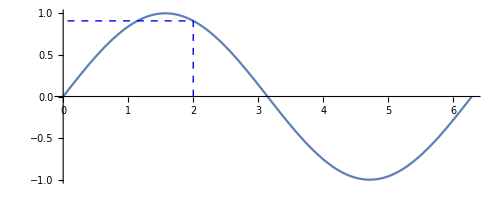

```mathematica
Plot[Sin[x],{x,0,2π},AspectRatio->Automatic,Epilog->{Directive[Dashed,Blue],Line[{{2,0},{2,Sin[2]},{0,Sin[2]}}]}]
```

```mathematica
Manipulate[Plot[Sin[t],{t,0,2π},Ticks->{Range[0,2π,π/6],Sin[Range[-π/2,π/2,π/6]]},Epilog->{{Dashed,Line[{{x,0},{x,Sin[x]},{0,Sin[x]}}]},{Red,PointSize[.015],Point[{x,Sin[x]}]}}],{{x,(2π)/3},0,2π}]
```

## 커피의 온도 변화 함수 구하기

다음 데이터는 컵에 담긴 커피의 온도를 시간에 따라 측정한 값이다.

```mathematica
data={{0, 149.5}, {2, 141.7}, {4, 134.7}, {6, 128.3}, {8, 122.6}, {10, 117.4}, {12, 112.7}, {14, 108.5}, {16, 104.7}, {18, 101.3}, {20, 98.2}, {22, 95.4}, {24, 92.9}, {26, 90.5}, {28, 88.5}, {30, 86.6}};
```

```mathematica
data
```

{{0,149.5},{2,141.7},{4,134.7},{6,128.3},{8,122.6},{10,117.4},{12,112.7},{14,108.5},{16,104.7},{18,101.3},{20,98.2},{22,95.4},{24,92.9},{26,90.5},{28,88.5},{30,86.6}}

ListPlot 명령은 쌍으로 엮인 데이터의 그래프를 그려준다.

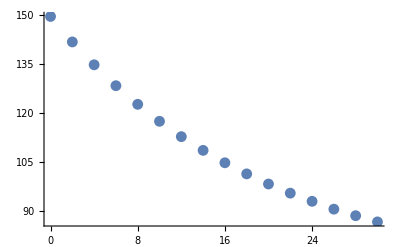

```mathematica
ListPlot[data]
```

먼저 간단한 함수로 시작해 본다.

```mathematica
fitLine=Fit[data,{1,x},x]
```

141.332-2.03257 x

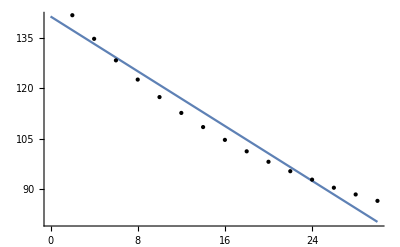

```mathematica
Plot[fitLine,{x,0,30},Epilog->Point[data]]
```

온도가 높을 땐 급격히 식다가, 주변 온도와 비슷해지면 식는 속도가 감소할 것 같다.

```mathematica
fitQuadratic=Fit[data,{1,x,x^2},x]
```

148.465-3.56107 x+0.0509498 x^2

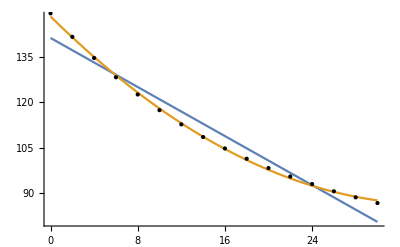

```mathematica
Plot[{fitLine,fitQuadratic},{x,0,30},Epilog->Point[data]]
```

### 리스트

```mathematica
myList=Table[2^k,{k,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

리스트의 다섯 번째 항목을 뽑아내려면,

```mathematica
{myList[[5]],myList⟦5⟧,myList_⟦5⟧}
```

{32,32,32}

리스트의 인덱스에 음수를 넣으면 리스트 끝에서부터의 순서를 나타낸다.

```mathematica
myList[[-2]]
```

512

리스트의 일부분을 뽑아내려면,

```mathematica
myList[[1;;4]]
```

{2,4,8,16}

편의상 맨 앞과 뒤를 지칭하는 명령이 있다.

```mathematica
{First[myList],Last[myList]}
```

{2,1024}

매스매티카의 거의 모든 수치연산 명령은 Listable 속성을 갖는다.

```mathematica
{1,2,3,4}+1
```

{2,3,4,5}

```mathematica
2*myList
```

{4,8,16,32,64,128,256,512,1024,2048}

```mathematica
Log[2,myList]
```

{1,2,3,4,5,6,7,8,9,10}

명령이 Listable 속성을 보유하고 있는지 확인하려면,

```mathematica
??Log
```

Log[z] gives the natural logarithm of z (logarithm to base e). 
Log[b,z] gives the logarithm to base b.

Attributes[Log]={Listable,NumericFunction,Protected}
 
Log/:MakeBoxes[Log[BoxForm`b_,BoxForm`z_],TraditionalForm]:=RowBox[{SubscriptBox[log,MakeBoxes[BoxForm`b,TraditionalForm]],(,MakeBoxes[BoxForm`z,TraditionalForm],)}]

2차원 데이터는 2중 리스트 구조로 저장된다.

```mathematica
data={{1, 214}, {11, 378}, {21, 680}, {31, 1215}, {41, 2178}, {51, 3907}};
```

3행 2열의 원소를 얻으려면:

```mathematica
data[[3,2]]
```

680

2열 전체를 뽑아내려면:

```mathematica
data[[All,2]]
```

{214,378,680,1215,2178,3907}

또는

```mathematica
data[[;;,2]]
```

{214,378,680,1215,2178,3907}

2열에만 로그를 적용하려고 한다면:

```mathematica
newData=data;
newData[[All,2]]=Log[data[[All,2]]];
newData//Grid
```

1 | Log[214]
11 | Log[378]
21 | Log[680]
31 | Log[1215]
41 | Log[2178]
51 | Log[3907]

다른 방법으로는

```mathematica
Transpose[{data[[All,1]],Log[data[[All,2]]]}]//Grid
```

1 | Log[214]
11 | Log[378]
21 | Log[680]
31 | Log[1215]
41 | Log[2178]
51 | Log[3907]

## 점화식

Piecewise 명령을 이용하여 수열을 정의할 수 있다.

```mathematica
Clear[s,n];
s[n_Integer]:=Piecewise[{{s[1]=3, n==1}, {s[n]=2s[n-1], n>1}}]
```

```mathematica
s[4]
```

24

저장된 s를 확인해보면,

```mathematica
?s
```

Global`s

s[1]=3
 
s[2]=6
 
s[3]=12
 
s[4]=24
 
s[n_Integer]:=Piecewise[{{s[1]=3,n==1},{s[n]=2 s[n-1],n>1}}]

모든 s[_]는 s에 연관되어 있는 걸 확인할 수 있다.

```mathematica
Clear[s]
```

```mathematica
?s
```

Global`s

다른 수열을 정의해보면,

```mathematica
Clear[s];
s[n_Integer]:=Piecewise[{{s[1]=2, n==1}, {s[n]=3s[n-1]-.05 s[n-1]^2, n>1}}]
```

```mathematica
Clear[t];
t[n_Integer]:=Piecewise[{{2, n==1}, {3t[n-1]-.05 t[n-1]^2, n>1}}]
```

```mathematica
Timing[s[20]]
```

{0.,37.0838}

```mathematica
Timing[t[20]]
```

{8.71151,37.0838}

```mathematica
s[2000]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

$Aborted

재귀적 명령의 호출 횟수는 $RecursionLimit 번으로 제한되어 있다.

```mathematica
$RecursionLimit
```

1024

```mathematica
Table[s[n],{n,1000,2000,1000}]
```

{39.5505,39.6823}

## 외부 정보 활용

대한민국의 인구는?

```mathematica
CountryData["SouthKorea","Population"]
```

4.87748×10^7

```mathematica
CountryData["SouthKorea",{"Population",1970}]
```

3.1443×10^7

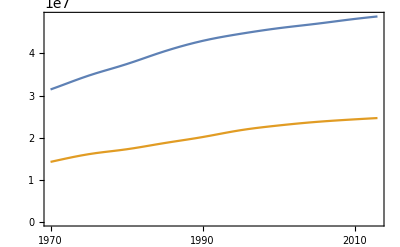

```mathematica
DateListPlot@{
Tooltip[
CountryData["SouthKorea",{"Population",{1970,2014}}],
"South Korea"
],
Tooltip[
CountryData["NorthKorea",{"Population",{1970,2014}}],
"North Korea"
]
}
```

우리나라의 국내 총생산은

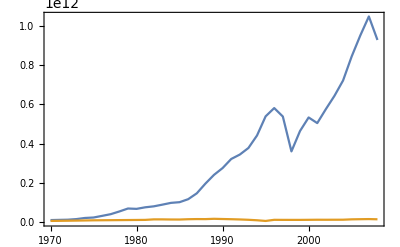

```mathematica
DateListPlot@{
Tooltip[
CountryData["SouthKorea",{"GDP",{1970,2014}}],
"South Korea"
],
Tooltip[
CountryData["NorthKorea",{"GDP",{1970,2014}}],
"North Korea"
]
}
```

세계의 석유 사용량은

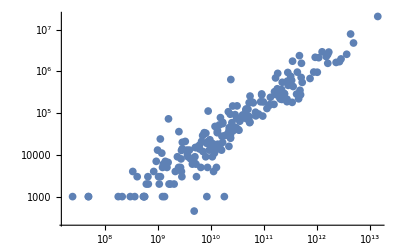

```mathematica
ListLogLogPlot[Table[Tooltip[{CountryData[c,"GDP"],CountryData[c,"OilConsumption"]},CountryData[c,"Name"]],{c,CountryData[]}]]
```